```mathematica
ClearAll["Global`*"]
```

```mathematica
tableS = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\SeriesCircut_2019_09_03_15_08_01.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtableS = Delete[tableS, 1];
```

```mathematica
ZparallelRC[R_, C_, ω_] := (R×1/(ⅈ×ω×C))/(R+1/(ⅈ×ω×C))
```

```mathematica
ZparallelRL[R_,L_,ω_]:=(R×ⅈ×ω×L)/(R+ⅈ×ω×L)
Zparallel2[R1_,R2_]:=(R1×R2)/(R1+R2)
```

```mathematica
Zparallel3[R1_, R2_, R3_]:= (R1×R2×R3)/(R1×R2+R2×R3+R3×R1)
```

```mathematica
ZS[ω_,C0_,L_,Rp_,Cp_]:=50+1/(ⅈ×ω×C0)+Zparallel3[50×10^3, (ⅈ×ω×L+0.5+ZparallelRL[Rp,0.0011,ω]), (1/(ⅈ×ω×Cp))]+ZparallelRC[46.5, 25×10^-12, ω]
```

```mathematica
Uin[ω_,C0_,L_,Rp_,Cp_]:=2*Re[Abs[ZparallelRC[46.5, 25*10^-12, 2π×ω]]/Abs[ZS[2π×ω,C0,L,Rp,Cp]]]
```

```mathematica
fitS = FindFit[newtableS, Uin[ω,C0,L,Cp], {{C0,150×10^-12},{L, 2.03×10^-3}, {Cp, 4.52×10^-11},{Rp,200}}, ω, MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{C0→1.48017×10^-10,L→0.00202896,Cp→4.31745×10^-11,Rp→200.}

```mathematica
nlm=NonlinearModelFit[newtableS, Uin[ω,C0,L,Cp], {{C0,150×10^-12},{L, 2.03×10^-3}, {Cp, 4.52×10^-11},{Rp,200}}, ω, MaxIterations->1000]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[5.92056×10^11 Re[Abs[1/((46.5-(20000000000 ⅈ)/(π ω)) ω)]/Abs[50-(«3»+«1»)/ω-(«1»)/(«1»)-((0.+1.84316×10^14 ⅈ) («1»))/(ω (-(0.+«22» ⅈ)/ω+50000 («1»)-((«1»)«1»(«1»«1»)/ω))]]]

```mathematica
nlm["ParameterConfidenceIntervals"]
```

General::munfl: 0.00307952^623. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1.37551×10^-10,1.58483×10^-10},{0.00202765,0.00203028},{3.11212×10^-11,5.52278×10^-11},{200.,200.}}

```mathematica
FindMinimum[Uin[ω,C0,L,Cp]/.fitS,{ω,500000}]
```

{0.00213516,{ω→537791.}}

```mathematica
FindMaximum[Uin[ω,C0,L,Cp]/.fitS,{ω,300000}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.120533,{ω→253707.}}

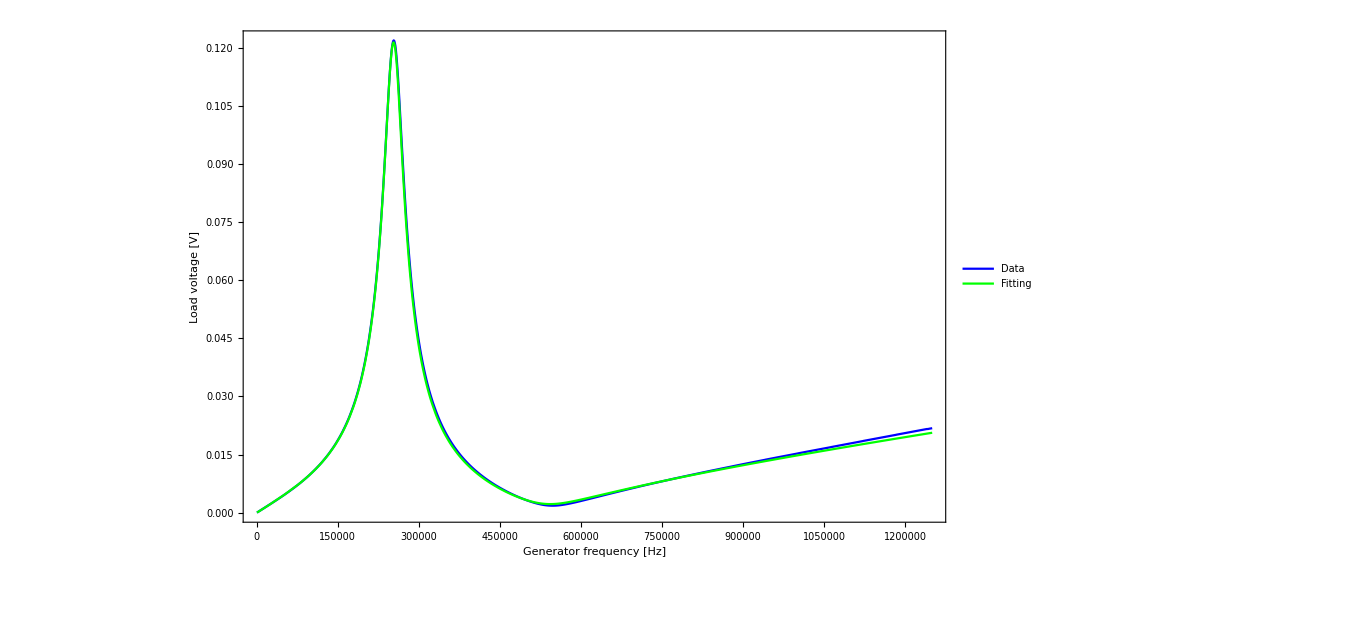

```mathematica
Legended[Show[ListLinePlot[newtableS, PlotStyle->Blue, PlotRange->Full],
Plot[Uin[ω,C0,L,Cp]/.fitS,{ω,Min[newtableS[[All,1]]],Max[newtableS[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
tableP = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\ParallelCircut_2019_09_03_15_23_37.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtableP = Delete[tableP,1];
```

```mathematica
ZP[ω_,C0_,L_,Rp_,Cp_]:=50+ZparallelRC[46.5, 25×10^-12, ω]+Zparallel2[(ⅈ×ω×9.83×10^-7+ZparallelRC[4.63×10^5, C0, ω]+48),(Zparallel3[50×10^3, (ⅈ×ω×L+0.5+ZparallelRL[Rp,0.0011,ω]), (1/(ⅈ×ω×Cp))])]
```

```mathematica
UinP[ω_,C0_,L_,Rp_,Cp_]:=2*Re[Abs[ZparallelRC[46.5, 25*10^-12, 2π×ω]]/Abs[ZP[2π×ω,C0,L,Rp,Cp]]]
```

```mathematica
fitP = FindFit[newtableP, UinP[ω,C0,L,Rp,Cp], {{C0,150×10^-12},{L, 2.03×10^-3},{Rp,145}, {Cp, 4.52×10^-11}}, ω, MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{C0→1.50173×10^-10,L→0.00209841,Rp→132.718,Cp→4.59818×10^-11}

```mathematica
FindMinimum[UinP[ω,C0,L,Rp,Cp]/.fitP,{ω,200000}]
```

{0.0034381,{ω→247949.}}

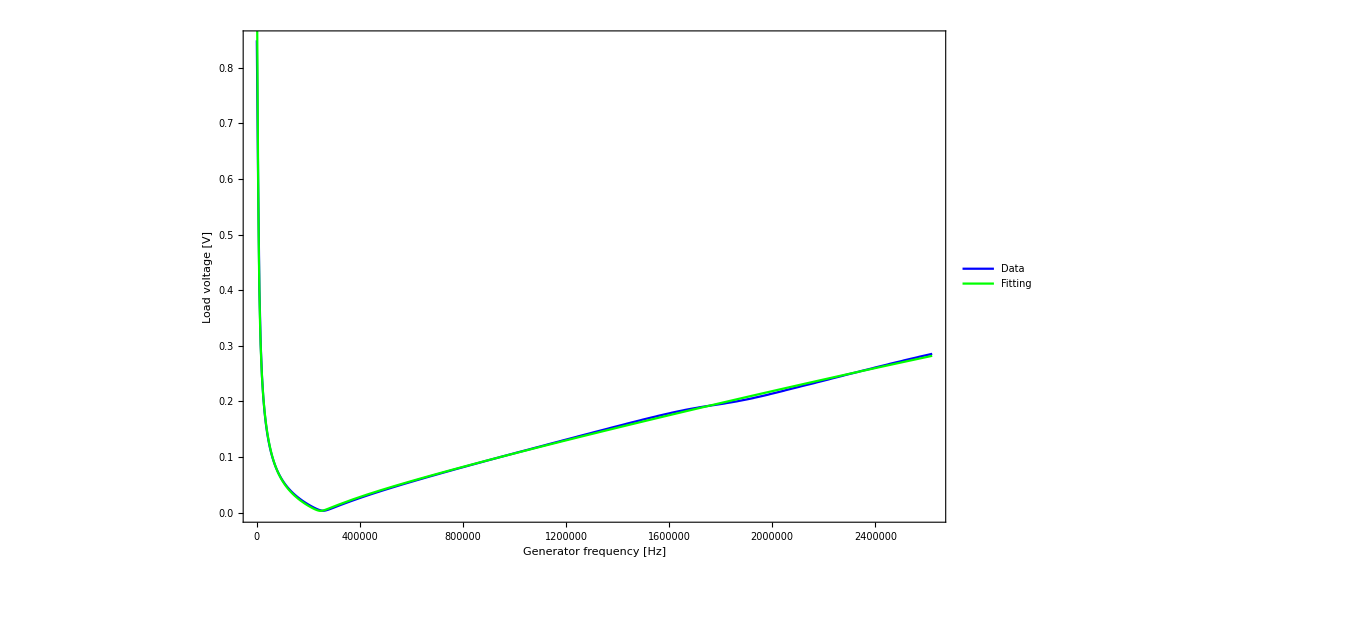

```mathematica
Legended[Show[ListLinePlot[newtableP, PlotStyle->Blue, PlotRange->Full],
Plot[UinP[ω,C0,L,Rp,Cp]/.fitP,{ω,Min[newtableP[[All,1]]],Max[newtableP[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```